```mathematica
ME314 Final Project;
FeiyuChen;
Scene2;
```

```mathematica
Quit[]
```

```mathematica
(*Open and run all other Mathematica scripts*)
myOpenFile[filename_]:=Module[{nb1},nb1=NotebookOpen[NotebookDirectory[]<>"/"<>filename];
     SelectionMove[nb1,All,Notebook];
     SelectionEvaluate[nb1]
]
myOpenFile["../funcs_math.nb"];
myOpenFile["../funcs_assist.nb"];
myOpenFile["../funcs_main.nb"];
(* !!!!!!!!! wait for 1 second before running the following !!!!!)
```

```mathematica
(*Put your code here to create links system*)
CreatePolygon[p0_,p1_,NumOfEdges_,DOF_]:=Module[{},
l=CalcDistpp[p0,p1];
If[DOF==0,
linki=createLink0DOFpp[p0,p1],
linki=createLink3DOFpp[p0,p1]];
For[i=1,i≤NumOfEdges-1,i=i+1,
linki=createLink0DOFgθl[linki[[IdxTFront]],2*Pi/NumOfEdges,l]
];
];
CreateObjects:=Module[{},

(* Object 1: Triangle *)
nthGroup=1;
initRandVelocity=0.5;
CreatePolygon[{-0.5,2.5},{0.1,2.7},3,3];

(* Objects 2: Walls *)
nthGroup=2;

CreatePolygon[{-4.5,1},{-3.5,1},4,0];
CreatePolygon[{-2.5,1},{-1.5,1},4,0];
CreatePolygon[{-0.5,1},{0.5,1},4,0];
CreatePolygon[{1.5,1},{2.5,1},4,0];
CreatePolygon[{3.5,1},{4.5,1},4,0];

(* Objects 3: Wall of Floor *)
createLink0DOFpp[{-20,0},{20,0}];
];
```

```mathematica
(* Set up all things *)
mainResetVars;
CreateObjects;
RemoveDuplicateVertexs;

externalForces=ConstantArray[0,nVars];

Print["\nStart Solving ..."];
mainSolveELeqs;
Print["Finish Solving ..."];

ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];

Print["\nStart setting impact ..."];
SetUpImpacts[];
Print["Finish setting impact ..."];
```

Start Solving ...

Finish Solving ...

Start setting impact ...

Finish setting impact ...

```mathematica
(* Set up params for NDSolve *)
timeend=15;(* total simulation time *)
MAXIMPACTTIMES=1000;
impactDetectionError=0.05;
intergrationMaxStepSize=0.001;
ifprint=False;

(* NDsolve and Play simulation *)
{end,data,bounces}=mainNDSolveSimulation[qsInit,dqsInit];
```

Computing simulation: 2.49177 / 15 ...

Computing simulation: 4.01558 / 15 ...

Computing simulation: 6.04709 / 15 ...

Computing simulation: 8.01852 / 15 ...

Computing simulation: 10.0067 / 15 ...

Computing simulation: 12.3332 / 15 ...

Computing simulation: 14.4877 / 15 ...

Computing simulation is completed.

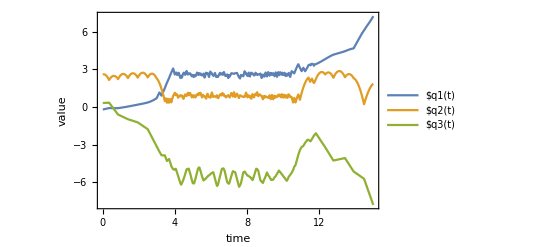

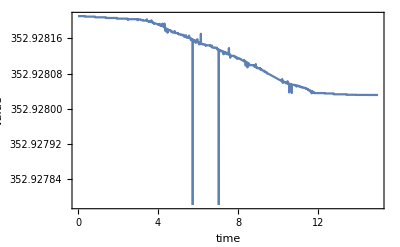

```mathematica
(* Plot *)
plotVariablesValues
plotHamValues
plotAnimation[{{-6,6},{-1,3}}]
```